```mathematica
sredno=Sqrt[Integrate[(x^2-x)^2,{x,0,1}]]
```

1/(√30)

```mathematica
ravnomerno = MaxValue[{Abs[x-x^2], 0≤ x-x^2≤1},x ]
```

1/4

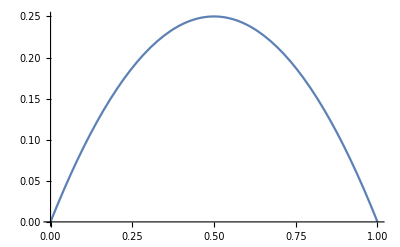

```mathematica
Plot[Abs[x-x^2],{x, 0,1}]
```

```mathematica
f[x_]=1/(1+25x^2)
```

1/(1+25 x^2)

```mathematica
p4[x_]=1-4.22719x^2+3.31565x^4
```

1-4.22719 x^2+3.31565 x^4

```mathematica
p10[x_]=1-16.8552x^2+123.36x^4-381.434x^6+494.91x^8-220.942x^10
```

1-16.8552 x^2+123.36 x^4-381.434 x^6+494.91 x^8-220.942 x^10

```mathematica
Ravno[f_,x_,a_,b_]:=MaxValue[{Abs[f[x]], a≤x≤b},x ]
```

```mathematica
Sredno[f_,x_,a_,b_]:=Sqrt[Integrate[(f[x])^2,{x,a,b}]]
```

```mathematica
diff4[x_]:=f[x]-p4[x]
```

```mathematica
diff10[x_]:=f[x]-p10[x]
```

```mathematica
r4=Ravno[diff4,x,-1,1]
```

0.406973

```mathematica
s4=Sredno[diff4,x,-1,1]
```

0.376033

```mathematica
r10=Ravno[diff10,x,-1,1]
```

1.91592

```mathematica
s10=Sredno[diff10,x,-1,1]
```

0.820905

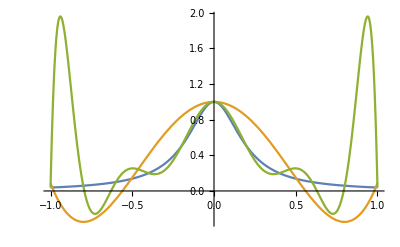

```mathematica
Plot[{f[x],p4[x],p10[x]}, {x, -1,1}]
```

```mathematica
g[x_]=E^x
```

ⅇ^x

```mathematica
h[x_]=a*x^2+b*x+c
```

c+b x+a x^2

```mathematica
diff[x_]=g[x]-h[x]
```

-c+ⅇ^x-b x-a x^2

```mathematica
ur[a_,b_,c_]=Sredno[diff,x,0,1.5]
```

√(9.54277+1.51875 a^2+1.125 b^2-6.96338 c+1.5 c^2+b (-6.48169+2.25 c)+a (-7.20422+2.53125 b+2.25 c))

```mathematica
sol=NSolve[{D[ur[a,b,c],a]==0,D[ur[a,b,c],b]==0,D[ur[a,b,c],c]==0},{a,b,c}]
```

{{a→1.1017,b→0.58595,c→1.05539}}

```mathematica
p[x]=h[x]/.sol[[1]]
```

1.05539+0.58595 x+1.1017 x^2

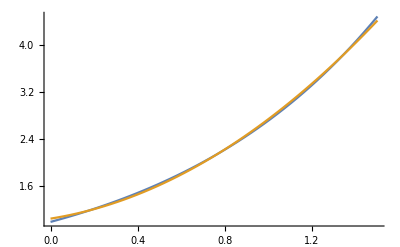

```mathematica
Plot[{E^x, 1.0553893075245833+0.5859497491819532 x+1.1016992366413263 x^2}, {x, 0, 1.5}]
```